```mathematica
Quit[]
```

Loading the variable Files

```mathematica
(*Choose folder, variables of interest and output file name*)
directory="C:\\Users\\Saba\\Desktop\\2019_02_Reactions\\ReactionsRP1200uW\\Reactions" ;(*Folder to analyse*)
outfile= "C:\\Users\\Saba\\Desktop\\2019_02_Reactions\\ReactionsRP1200uW\\NewAnalysis_V4\\Results\\data_mot_single_rp1200.dat";(*output-file*)
outfileMean ="C:\\Users\\Saba\\Desktop\\2019_02_Reactions\\ReactionsRP1200uW\\NewAnalysis_V4\\Results\\data_mot_meanrp1200.dat";
ofile = "C:\\Users\\Saba\\Desktop\\2019_02_Reactions\\ReactionsRP1200uW\\NewAnalysis_V4\\Results\\data_mot_mean_finalrp1200.dat";
motalldata="C:\\Users\\Saba\\Desktop\\2019_02_Reactions\\ReactionsRP1200uW\\NewAnalysis_V4\\Results\\mot_all_data_rp1200.dat";
varvar = {"MOTDu","FAbs","AbsDu"} ; (*Variables of interest from VariableValue file*)
datvar = {"PicoTOF_Ion"} ;(*Variables of interest from dataValue file*)
(*Load the folders*)
SetDirectory@directory
foldernames = Select[FileNames[],DirectoryQ];
Length@foldernames;
If[Length@foldernames==0,foldernames={directory}];
Length@foldernames
fnames = FileNames["*.dat",foldernames];
Length@fnames;
```

C:\Users\Saba\Desktop\2019_02_Reactions\ReactionsRP1200uW\Reactions

5

```mathematica
(*Put files in a table with their run number and typ*)
typTable = Table[{fnames[[n]],ToExpression@StringSplit[fnames[[n]],{foldernames,"\\","_","R",".dat"}][[1]],StringSplit[fnames[[n]],{foldernames,"\\","_","R",".dat"}][[2]]},{n,1,Length@fnames}];
(*seperate VariableValues and DataValues*)
varTable = Select[typTable,#[[3]]=="VariableValues"&];
datTable = Select[typTable,#[[3]]=="DataValues"&];
picoTable = Select[typTable,#[[3]]=="PicoTOF"&];
adcTable = Select[typTable,#[[3]]=="ADC"&];

(*Check if output exists and get last evaluated run*)
If[FileExistsQ[outfile],
lrun = Max[Import[outfile][[2;;-1,1]]];,
lrun = Min[datTable[[All,2]]];
]

"Last run = "<>ToString@lrun
```

Last run = 8823

```mathematica
getvarvalues[n_, var_]:=Module[{fname,firstRun,datafile,run,value,ncol,out},
fname = varTable[[n,1]];
firstRun = varTable[[n,2]];
datafile = Import[fname,NumberPoint->","];
ncol = Flatten[Position[datafile,"Run#"]][[2]];
out = {ToExpression@datafile[[2;;-1,ncol]]+firstRun};
(*Loop trough variables of interest*)
For[i=1,i≤ Length@var,i++,
ncol = Flatten[Position[datafile,var[[i]]]][[2]]; (*Find value*)
If[!NumericQ[ncol],
AppendTo[out,"NaN"];,
AppendTo[out,ToExpression@datafile[[2;;-1,ncol]]] ; 
]
];
Return[Transpose@out];
]
getdatvalues[n_,var_]:=Module[{fname,datafile,run,nrow, out},
fname = datTable[[n,1]];
datafile = Import[fname,NumberPoint->","];
run = ToExpression@datTable[[n,2]];
out = {run};
AppendTo[out,AbsoluteTime[FileDate[fname,"Modification"]]];
For[i=1,i≤ Length@var,i++,
nrow = Flatten[Position[datafile,datvar[[i]]]][[1]];
If[!NumericQ[nrow],
AppendTo[out,"NaN"];,
AppendTo[out,datafile[[nrow,-1]]];
]
];
Return[out];
]

getadcvaluesmean[n_]:= Module[{fname,run,data,datafile,nrows,row,t,pos,mean,std,out},
out ={};
fname = adcTable[[n,1]];
datafile = Import[fname,NumberPoint->","];
nrows = Length@datafile/3;
For[row=1,row≤ nrows,row++,
run = ToExpression@StringSplit[datafile[[((row-1)*3)+1]],"#RunR"][[1,1]];
data = Select[Transpose@datafile[[((row-1)*3)+2;;((row-1)*3)+3,2;;-1]],#[[2]]>0.25&];
If[Length@data>0,
t =data[[-1,1]]- data[[1,1]];
mean = Mean@data[[All,2]];
std = StandardDeviation@data[[All,2]];,
t=0;
mean = 0;
std = 0;
];
out = Append[out,{run,mean,std,t}]
];
Return[out];
]
combine[n_] :=Module[{valuesvar,valuesdat,valuesadc,out},
valuesvar =Flatten@Select [outvarTable, #[[1]]==outdatTable[[n,1]]&];
valuesdat = outdatTable[[n]];
out= Flatten@{valuesvar,valuesdat};
Return[out];
]
```

```mathematica
(*Find position of last run*)
lrun
poslrun = Flatten[Position[datTable[[All,2]],Nearest[datTable[[All,2]],lrun][[1]]]][[1]]
(*Make a table of new dat values --> from last run safed in out file to last measured file*)
"Make a table of new dat values"
Length@datTable
Monitor[outdatTable = Table [getdatvalues[n,datvar],{n,1,Length@datTable}];,n]

(*Make a table of var values*)

"Make a table of var values"
(*poslrun = Flatten[Position[adcTable,Nearest[Select[adcTable,#[[2]]≤lrun&][[All,2]],lrun][[1]]]][[1]];*)
outvarTable = getvarvalues[1,varvar];
Length@varTable
Monitor[outvarTable = Table[getvarvalues[n,varvar],{n,1,Length@varTable}],n];
outvarTable = Flatten[outvarTable,1];
```

8823

1

Make a table of new dat values

1300

Make a table of var values

5

```mathematica
(*Combining and exporting*)
Length@outdatTable;
Monitor[outTable = Table[combine[n],{n,1,Length@outdatTable}];,n]
header = Flatten@{"#Run",varvar,"#Run","Time",datvar};

If[FileExistsQ[outfile],
table = Import[outfile];
outTable=Join[table,outTable];
Export[outfile,outTable],
PrependTo[outTable,header];
Export[outfile,outTable]
]

motpos = Position[outTable,"MOTDu"][[1,2]];
ionpos = Position[outTable,"PicoTOF_Ion"][[1,2]];
detpos = Position[outTable,"FAbs"][[1,2]];
imgdupos = Position[outTable,"AbsDu"][[1,2]];
```

C:\Users\Saba\Desktop\2019_02_Reactions\ReactionsRP1200uW\NewAnalysis_V4\Results\data_mot_single_rp1200_1.dat

```mathematica
SetDirectory@directory;
variableData=Import[outfile][[2;;]];
exposureTime=Mean@variableData[[All,imgdupos]]*1000;
detuning1=variableData[[All,detpos]];
(*to get exposure time in micro seconds*)
```

Absorption Images

```mathematica
(*Importing the imgae files from different folders here *)

fnamesMot11 = Table[FileNames["*.bmp",foldernames[[n]]],{n,1,Length@foldernames}];
Length@foldernames
Length@fnames
```

5

1310

```mathematica
(*Structure of Table --> Filename, Run Number, Kind*)
mottable1= Table[{fnamesMot11[[m,n]],ToExpression@StringSplit[fnamesMot11[[m,n]],{foldernames[[m]],"\\","_","R",".bmp"}][[1]],StringSplit[fnamesMot11[[m,n]],{foldernames[[m]],"\\","_","R",".bmp"}][[-1]]},{m,1,Length@foldernames},{n,1,Length@fnamesMot11[[m]]}];
mottable=Flatten[mottable1,1];
firstrun1 = Min@mottable1[[All,All,2]];
lastrun1= Max@mottable1[[All,All,2]];
firstruns =Table[Min@mottable1[[n,All,2]],{n,1,Length@foldernames}]
lastruns =Table[Max@mottable1[[n,All,2]],{n,1,Length@foldernames}]
"Runs = "<>ToString[lastrun1-firstrun1]
"First File = "<> ToString[fnamesMot11[[1,1]]]
absCrossSection=2.907*10^-13 (*  in m From Daniel A. Steck Rb-85 *);  
pixelSizeY=9.8*10^-3*2;(*In mm. Factor 2 comes from video mode. 2x2 pixels are binned*)
pixelSizeX=8.4*10^-3*2;
pixelArea=pixelSizeX pixelSizeY/100;
magnification=0.5; 
pi=3.14159265359;
β=0.0185; (*in signal/(nW µs), see FinalIntensityClaibrationv7.nb*)
t0=0.1755; (*in µs, see FinalIntensityClaibrationv7.nb*)
(*attenuation=0.5;*)
sat0Intensity=1.67 ; 
alpha=3.2;
```

{8823,9083,9343,9603,9863}

{9082,9342,9602,9862,10122}

Runs = 1299

First File = 2019-02-15_11-38-13_ReactionsRP1200uW\R8823_C0_cam__Abs.bmp

```mathematica
(* Functions  *)
(*detuning*)
(*DetuningFactor[x_]:=Module[{lw,x0,fabs,fabs0,fdetun,a1},
lw = 2*3.825; (*From the Analysis of Detuning Factor \\axion\qd-local\qd\HAITrap\Auswertung-analysis\2018_08_06_DetuningFactor\Analysis *)
x0 =5.071; (* Voltage for AMO @ resonance Transition*)
fabs=2*( -4.29674*x+113.662);
fabs0=2*( -4.29674*x0+113.662); 
(*  2 for double-pass AOM Function from Labview Program, convert from Volt to AMO Frequenzy*)
fdetun= (fabs-fabs0)/lw; 
a1= (1+4*(fdetun)^2);
Return[a1];
];*)
DetuningFactor2[x_]:=Module[{lw,x0,fabs,fabs0,fdetun,a1},
lw = 3.856; (*From the Analysis of Detuning Factor \\axion\qd-local\qd\HAITrap\Auswertung-analysis\2018_08_06_DetuningFactor\Analysis *)
x0 =5.071; (* Voltage for AMO @ resonance Transition*)
fabs=( -4.122*x+112.9);
fabs0=( -4.122*x0+112.9); 
(*  2 for double-pass AOM Function from Labview Program, convert from Volt to AMO Frequenzy*)
fdetun= (fabs-fabs0)/lw; 
a1= lw*(1+4*(fdetun)^2)/4;
Return[a1];
];
```

91.9973

```mathematica
(*Import pics in terms of Graylevels*)
ImportImages[n_]:={
Import[Select[mottable,#[[2]]==n&& #[[3]]=="Abs"&][[1,1]],"GrayLevels"],
Import[Select[mottable,#[[2]]==n&& #[[3]]=="Div"&][[1,1]],"GrayLevels"],
Import[Select[mottable,#[[2]]==n&& #[[3]]=="Bgd"&][[1,1]],"GrayLevels"],
Import[Select[mottable,#[[2]]==n&& #[[3]]=="Bgd2"&][[1,1]],"GrayLevels"]
}
(*Converting the pixels in the image sinto the x and y values*)
PixelsToPosition[data_]:=Array[{(#2 pixelSizeX)/magnification,(#1 pixelSizeY)/magnification,data[[#1,#2]]}&,Dimensions[data]];
(*Binning: To smoothen the images*)
Binning[data_,bin_]:=Module[{max,testbin},
max=Floor[(Dimensions[data][[1;;2]])/bin]-1;
testbin=Table[Mean@Flatten[data[[bin y+1;;bin(y+1),bin x+1;;bin(x+1),All]],1],{y,0,max[[1]]},{x,0,max[[2]]}];
Return[testbin];
];


(*Function to Convert the Intensity into the GrayScale values*)
IntensityToAmplitude[intensity_,exposureTime_]:=10^6 pixelArea(β(exposureTime-t0))/magnification^2 intensity;
(*Calculating the optical depth*)
(*optDepth[n_,alpha_,varnum_]:=Module[{data2,texp,pos1},
 texp=exposureTime; (*varnum is the variable used for extracting the value of a parameter at a particular run number (1,2,3...,Numberofruns)*)
data2=ImportImages[n];  (*n is the variable used for extracting the images, it uses run number (firstrun,....)*)
data2=-alpha*Log[(data2[[1]]-data2[[4]]+0.00001)/(data2[[2]]-data2[[3]]+0.00001)]+255*((data2[[2]]-data2[[3]]-(data2[[1]]-data2[[4]])))/(attenuation*IntensityToAmplitude[sat0Intensity,texp]); 
For[i=1,i≤Length@data2,i++, (*Replace complex number by 0*)
If[Length@Select[data2[[i]],Im[#]≠ 0&]>0, (*Are complex numbers in the Line i*)
pos1 = Flatten@Position[data2[[i]],Alternatives@@Select[data2[[i]],Im[#]≠ 0&]]; (*get position of complex numbers in the Line i*)
data2[[i,pos1]]=0 ; (*Set them to 0*)
];
];
Return[data2];
];
*)
optDepth2[n_,alpha_,varnum_]:=Module[{data2,texp,pos1},
 texp=exposureTime; (*varnum is the variable used for extracting the value of a parameter at a particular run number (1,2,3...,Numberofruns)*)
data2=ImportImages[n];  (*n is the variable used for extracting the images, it uses run number (firstrun,....)*)
data2=-alpha*DetuningFactor2[Select[variableData,#[[1]]==n&][[1,detpos]]]*Log[(data2[[1]]-data2[[4]]+0.00001)/(data2[[2]]-data2[[3]]+0.00001)];
For[i=1,i≤Length@data2,i++, (*Replace complex number by 0*)
If[Length@Select[data2[[i]],Im[#]≠ 0&]>0, (*Are complex numbers in the Line i*)
pos1 = Flatten@Position[data2[[i]],Alternatives@@Select[data2[[i]],Im[#]≠ 0&]]; (*get position of complex numbers in the Line i*)
data2[[i,pos1]]=0 ; (*Set them to 0*)
];
];
Return[data2];
];

(*Fitting Algorithm*)
PerformFitpod[data_]:=Module[{fit,height,sigmaX,sigmaY,sigmaZ,peakDensity,fp,volume,evolume,atomNumber,atomDensity1,eAD1,fe,eAN,eAD,atomDensity,posValue,out,gaussCenter},
(*Starting values for position and height of the gaussian*)
gaussCenter =data[[Flatten[Position[data,Max@data[[All,3]]],1][[1]]]];
fit=NonlinearModelFit[data,{a Exp[-((y-my)Cos[ϕ]-(x-mx)Sin[ϕ])^2/(2 σy^2)-((x-mx)Cos[ϕ]+(y-my)Sin[ϕ])^2/(2 σx^2)]},{{a,gaussCenter[[3]]},{ϕ,0},{mx,gaussCenter[[1]]},{my,gaussCenter[[2]]},{σx,0.5},{σy,0.5}},{x,y},MaxIterations->20000];
fp=fit["BestFitParameters"];
fe=fit["ParameterErrors"];
height=fp[[1,2]];(*Extracting Peak Optical Density from the fits  *)
sigmaX=fp[[5,2]];(*Extracting Spread in x-direction from the fits in mm *)
sigmaY=fp[[6,2]];(*Extracting Spread in y-direction from the fits in mm *)
sigmaZ=fp[[5,2]];(*Spread in z-direction assumed to be same as in x-direction*)
atomNumber=2*pi*height*sigmaX(*mm*)*sigmaY(*mm*)/(absCrossSection*10^6);(*cross-section in mm^2*)
atomDensity=atomNumber*10^3/(CubeRoot[2*pi]*fp[[5,2]]*fp[[6,2]]*fp[[5,2]]);
atomDensity1=height*10^3(*Change from mm^3 to cm^3 *)/(Sqrt[2*Pi]*sigmaZ(*mm*)*absCrossSection*10^6) (*cross-section in mm^2*);
volume=(CubeRoot[2*pi]*fp[[5,2]]*fp[[6,2]]*fp[[5,2]])/10^3;
evolume=CubeRoot[2*pi]/10^3*Sqrt[(sigmaX*sigmaY*fe[[5]])^2+(sigmaZ*sigmaY*fe[[5]])^2+(sigmaX*sigmaZ*fe[[6]])^2];(*Standard Error Propagation for Volume *)eAN=(2*pi/(absCrossSection*10^6))*Sqrt[(sigmaX*sigmaY*fe[[1]])^2+(sigmaX*height*fe[[6]])^2+(height*sigmaY*fe[[5]])^2];(*Standard Error Propagation for Atom NUmbers *)
eAD= 10^3/(CubeRoot[2*pi])*Sqrt[(eAN/(sigmaX*sigmaY*sigmaZ))^2+(atomNumber*fe[[5]]/(sigmaX^2*sigmaY*sigmaZ))^2+(atomNumber*fe[[5]]/(sigmaZ^2*sigmaY*sigmaX))^2+(atomNumber*fe[[6]]/(sigmaX*sigmaY^2*sigmaZ))^2] ;
eAD1= (10^3/(Sqrt[2*Pi]*absCrossSection*10^6))*Sqrt[(fe[[1]]/sigmaZ)^2+(height*fe[[5]]/sigmaZ^2)^2];
(*Standard Error Propagation for Atom Density *)
out = {fit,fit["BestFitParameters"],fit["ParameterErrors"],atomNumber,eAN,atomDensity1,eAD1,volume,evolume};

Return[out];

];
```

```mathematica
(*test*)

bin1=4;
n = firstrun1;
testvalues = optDepth2[n,alpha,2];
testvalues=PixelsToPosition[testvalues];
testvalues=Binning[testvalues,bin1];
testvalues=Flatten[testvalues,1];
testvalues=Select[testvalues,#[[2]]<3.45&&#[[2]]>0.75&][[All]];
testvalues=Select[testvalues,#[[1]]<2.25&&#[[1]]>0.25&][[All]];   (*these steps can be used if you want to consider only part of images, a range can be plot and check*)
Max@testvalues[[All,3]]
gaussCenter =testvalues[[Flatten[Position[testvalues,Max@testvalues[[All,3]]],1][[1]]]]
result = PerformFitpod[testvalues]
Length@result;
result[[2,All,1]];(*Labels of the Fit parameters*)
result[[2,All,2]]; (*height/Peak Optical Density*)
result[[3,All]]; (*Error on the Fit parameters*)
result[[4]]; (*Atom Number*)
result[[5]]; (*Atom Density*)
fitvalues = result[[1,1,2]];
fitfunc = result[[1]];
xmin = Min@testvalues[[All,1]];
xmax = Max@testvalues[[All,1]];
ymin = Min@testvalues[[All,2]];
ymax = Max@testvalues[[All,2]];

Show[Plot3D[fitfunc[x,y],{x,xmin,xmax},{y,ymin,ymax},PlotRange->All],ListPointPlot3D[testvalues,ColorFunction->"Rainbow"]]
```

43.8736

{1.0248,2.45,43.8736}

{FittedModel[40.4442 ⅇ^(-6.60696 (0.872447 (-1.06869+x)-«1»)^2-4.4518 («19» («1»)+«1»)^2)],{a→40.4442,ϕ→-0.510608,mx→1.06869,my→2.37011,σx→0.275096,σy→0.335133},{0.788531,0.0694525,0.00566351,0.00626991,0.00536994,0.00653333},8.05922×10^7,2.72255×10^6,2.01761×10^11,5.56642×10^9,0.0000468,1.58162×10^-6}

-Graphics3D-

```mathematica
(*Get Table of the Peak Optical dnesities, atom number, atom densities.*)
(*Specify Bins*)
getpod[run_,binvalue_,alpha_,varn_]:=Module[{values,result,out},
values = optDepth2[run,alpha,varn];
values=PixelsToPosition[values];
values=Binning[values,binvalue];
values=Flatten[values,1];
values=Select[values,#[[2]]<3.45&&#[[2]]>0.75&][[All]];
values=Select[values,#[[1]]<2.25&&#[[1]]>0.25&][[All]];
If [Length@Select[values,Im[#[[3]]]≠ 0&]≠0, 
out ={run,"complex","number"};,
result = PerformFitpod[values];
If[Length@result>1,
out = Flatten@{run,result[[2,All,2]] ,result[[3,All]],result[[4]],result[[5]],result[[6]],result[[7]] ,result[[8]],result[[9]]};,
out = Flatten@{run, ToString@result};
];
];
Return[out];
];

"First run = " <> ToString[firstrun1];
"Last run = " <> ToString[lastrun1];
runlist =Tally[mottable[[All,2]]][[All,1]];
data11=Import[outfile][[2;;-1]]
Length@runlist;
```

{{8823.,1200.,6.3,0.05,8823,3759223121,0.},{8824.,0.,6.3,0.05,8824,3759223141,20.},{8825.,1050.,6.3,0.05,8825,3759223161,1.},{8826.,150.,6.3,0.05,8826,3759223181,6.},{8827.,1800.,6.3,0.05,8827,3759223201,1.},{8828.,150.,6.3,0.05,8828,3759223221,19.},{8829.,1200.,6.3,0.05,8829,3759223241,0.},{8830.,0.,6.3,0.05,8830,3759223261,24.},1285,{9993.,450.,6.3,0.05,9993,3759246632,18.},{9994.,600.,6.3,0.05,9994,3759246652,3.},{9995.,1650.,6.3,0.05,9995,3759246672,0.},{9996.,1650.,6.3,0.05,9996,3759246692,0.},{9997.,1350.,6.3,0.05,9997,3759246712,0.},{9998.,0.,6.3,0.05,9998,3759246732,21.},{9999.,750.,6.3,0.05,9999,3759246752,2.}}
 |  |  |  |

```mathematica
runlistnew=runlist;
For[i=1,i≤ Length@runlist,i++,
If[data11[[i,2]]==0.,runlistnew[[i]]=0,runlistnew[[i]]=runlist[[i]]];
];
runlistnew1=DeleteCases[_0][runlistnew];
(*NOT fitting the runs where MOT duration was zero to save calculation time*)
```

```mathematica
Clear[finaltable];
bin=3;
counter=0;
SetSharedVariable[counter];
PrintTemporary[Dynamic["Percent Completed: "<>ToString[N[(counter*100)/Length@runlistnew1]]]];

finaltable=Monitor[ParallelTable[counter++;
getpod[runlistnew1[[n]],bin,alpha,n],{n,1,Length@runlistnew1}],ProgressIndicator[counter/Length@runlistnew1]];

dateString = ToString@DateList[][[1]]<>"_"<>ToString@DateList[][[2]]<>"_"<>ToString@ DateList[][[3]]<>"-";
PrependTo[finaltable,{"run","a","phi","mx","my","sigmax","sigmay","ea","ephi","emx","emy","esigmax","esigmay","atomNumber","eAtomNumber","atomDensity","eAtomDensity","Volume","ErrorVolume"}];
(*Mention the name of the file you want to export the results to here*)
```

```mathematica
Export[motalldata,finaltable];
```

Sorting and Combining MOT Data for each MOTDu

```mathematica
(*Variable Data from the varibale files *)
data=Import[outfile][[2;;]]; 
Length@data
(*Fit results for MOT parameters for each run *)
MOTdata=finaltable[[2;;-1]];
Length@MOTdata
```

1300

1200

```mathematica
(*combine the  information from respective variable values and .dat files*)
MOTdatacombined =Table[Flatten@{Select[data,#[[1]]== MOTdata[[n,1]]&][[1,{1,2,3,4,5}]],MOTdata[[n,{2,6,12,7,13,14,15,16,17,18,19}]]},{n,1,Length@MOTdata}]
```

{{8823.,1200.,6.3,0.05,8823,40.6256,0.273848,0.00515442,0.334875,0.00630081,8.05243×10^7,2.62452×10^6,2.03589×10^11,5.41822×10^9,0.0000463406,1.51057×10^-6},1198,{9999.,750.,6.3,0.05,9999,31.094,0.239303,0.00599405,0.295517,0.00740191,4.75273×10^7,2.0619×10^6,1.78317×10^11,6.31648×10^9,0.0000312277,1.35478×10^-6}}
 |  |  |  |

```mathematica
(*Replace the values of atom numbers with zero where the fit did not converge, cases here if the POD and atom number is negative or the POD is greater than 20 (this number can be changed). or error of atom numbers i larger than the atom numbers*)
```

```mathematica
For[i=1,i≤Length@MOTdatacombined,i++,
Which[MOTdatacombined[[i,6]]<0,MOTdatacombined[[i,{6,7,8,9,10,11,12,13,14,15,16}]]=0,MOTdatacombined[[i,6]]>20000,MOTdatacombined[[i,{6,7,8,9,10,11,12,13,14,15,16}]]=0, MOTdatacombined[[i,7]]>2,MOTdatacombined[[i,{7,8,9,10,11,12,13,14,15,16}]]=0,MOTdatacombined[[i,7]]<MOTdatacombined[[i,8]],MOTdatacombined[[i,{7,8,9,10,11,12,13,14,15,16}]]=0,MOTdatacombined[[i,11]]<MOTdatacombined[[i,12]],MOTdatacombined[[i,{7,8,9,10,11,12,13,14,15,16}]]=0,MOTdatacombined[[i,13]]<MOTdatacombined[[i,14]],MOTdatacombined[[i,{7,8,9,10,11,12,13,14,15,16}]]=0];
];
```

```mathematica
MOTdataAll=Table[Select[MOTdatacombined,firstruns[[n]]≤ #[[1]]≤lastruns[[n]]&],{n,1,Length@foldernames}];
MOTdataAll[[2]];
```

```mathematica
(*Sorting through and arranging the data as per different Mot durations*)

motdurations=Table[Sort@DeleteDuplicates@MOTdataAll[[n,All,2]],{n,1,Length@MOTdataAll}];
indices=Table[Map[Flatten@Position[MOTdataAll[[n,All,2]],#]&,motdurations[[n]]],{n,1,Length@MOTdataAll}];

MOTDataSorted=Table[MOTdataAll[[n,indices[[n,m]]]],{n,1,Length@MOTdataAll},{m,Length@indices[[n]]}];
```

```mathematica
MOTTime=Table[motdurations[[n]]/1000,{n,1,Length@motdurations}];(*Converting ms to seconds*)
AtomNumberwithErr=Table[{Mean@MOTDataSorted[[n,m,All,2]]/1000,Mean@SparseArray[MOTDataSorted[[n,m,All,11]]]["NonzeroValues"],RootMeanSquare@SparseArray[MOTDataSorted[[n,m,All,12]]]["NonzeroValues"]},{n,1,Length@MOTdataAll},{m,1,Length@MOTTime[[n]]}];
```

```mathematica
(*Sorting Atom Numbers *)
AtomNumberwithErr=Table[{Mean@MOTDataSorted[[n,m,All,2]]/1000,Mean@SparseArray[MOTDataSorted[[n,m,All,11]]]["NonzeroValues"],RootMeanSquare@SparseArray[MOTDataSorted[[n,m,All,12]]]["NonzeroValues"]},{n,1,Length@MOTdataAll},{m,1,Length@MOTTime[[n]]}];

AtomNumberNoErr=Table[{Mean@MOTDataSorted[[n,m,All,2]]/1000,Mean@SparseArray[MOTDataSorted[[n,m,All,11]]]["NonzeroValues"]},{n,1,Length@MOTdataAll},{m,1,Length@MOTTime[[n]]}];
(*Sorting Atom Densities *)
AtomDensitywithErr=Table[{Mean@MOTDataSorted[[n,m,All,2]]/1000,Mean@SparseArray[MOTDataSorted[[n,m,All,13]]]["NonzeroValues"],RootMeanSquare@SparseArray[MOTDataSorted[[n,m,All,14]]]["NonzeroValues"]},{n,1,Length@MOTdataAll},{m,1,Length@MOTTime[[n]]}];(* from 2 to exclude zero*)
AtomDensityNoErr=Table[{Mean@MOTDataSorted[[n,m,All,2]]/1000,Mean@SparseArray[MOTDataSorted[[n,m,All,13]]]["NonzeroValues"]},{n,1,Length@MOTdataAll},{m,1,Length@MOTTime[[n]]}];

(*Sorting Atom Cloud Size-X *)
AtomSizeXwithErr=Table[{Mean@MOTDataSorted[[n,m,All,2]]/1000,Mean@SparseArray[MOTDataSorted[[n,m,All,7]]]["NonzeroValues"],RootMeanSquare@SparseArray[MOTDataSorted[[n,m,All,8]]]["NonzeroValues"]},{n,1,Length@MOTdataAll},{m,1,Length@MOTTime[[n]]}];(* from 2 to exclude zero*)
AtomSizeXNoErr=Table[{Mean@MOTDataSorted[[n,m,All,2]]/1000,Mean@SparseArray[MOTDataSorted[[n,m,All,7]]]["NonzeroValues"]},{n,1,Length@MOTdataAll},{m,1,Length@MOTTime[[n]]}];
(*Sorting Atom Cloud Size-Y *)
AtomSizeYwithErr=Table[{Mean@MOTDataSorted[[n,m,All,2]]/1000,Mean@SparseArray[MOTDataSorted[[n,m,All,9]]]["NonzeroValues"],RootMeanSquare@SparseArray[MOTDataSorted[[n,m,All,10]]]["NonzeroValues"]},{n,1,Length@MOTdataAll},{m,1,Length@MOTTime[[n]]}];(* from 2 to exclude zero*)
AtomSizeYNoErr=Table[{Mean@MOTDataSorted[[n,m,All,2]]/1000,Mean@SparseArray[MOTDataSorted[[n,m,All,9]]]["NonzeroValues"]},{n,1,Length@MOTdataAll},{m,1,Length@MOTTime[[n]]}];(* from 2 to exclude zero*)

(*Sorting Atom Cloud Volume*)
AtomVolumewithErr=Table[{Mean@MOTDataSorted[[n,m,All,2]]/1000,Mean@SparseArray[MOTDataSorted[[n,m,All,15]]]["NonzeroValues"],RootMeanSquare@SparseArray[MOTDataSorted[[n,m,All,16]]]["NonzeroValues"]},{n,1,Length@MOTdataAll},{m,1,Length@MOTTime[[n]]}];(* from 2 to exclude zero*)(* from 2 to exclude zero*)
AtomVolumeNoErr=Table[{Mean@MOTDataSorted[[n,m,All,2]]/1000,Mean@SparseArray[MOTDataSorted[[n,m,All,15]]]["NonzeroValues"]},{n,1,Length@MOTdataAll},{m,1,Length@MOTTime[[n]]}];
```

```mathematica
n=2
Flatten[AtomNumberwithErr,1][[n]];
Flatten[AtomDensitywithErr,1];
Flatten[AtomSizeXwithErr,1];
Flatten[AtomSizeYwithErr,1];
outfinalTable=Table[Flatten@{Flatten[AtomNumberwithErr,1][[n]],Flatten[AtomDensitywithErr,1][[n]],Flatten[AtomSizeXwithErr,1][[n]],Flatten[AtomSizeYwithErr,1][[n]]},{n,1Length@Flatten[AtomNumberwithErr,1]}];

PrependTo[outfinalTable,{"MOTDu","N","eN","MOTDu","rho","erho","MOTDu","sigmaX","esigmax","MOTDu","sigmay","esigmay"}];
Export[outfileMean,outfinalTable];
```

2

```mathematica
motraw=Import[outfileMean];
motrawT=motraw[[2;;-1]];

motpos = Position[motraw,"MOTDu"][[1,2]];
Npos = Position[motraw,"N"][[1,2]];
rhopos = Position[motraw,"rho"][[1,2]];
sigmaX = Position[motraw,"sigmaX"][[1,2]];
sigmaY = Position[motraw,"sigmay"][[1,2]];

mott = Sort@Tally[motrawT[[All,motpos]]][[All,1]];


getmean[data_,mott_]:=Module[{nt,out},
nt=Select[data,#[[motpos]]==mott&];
out = {
mott,
Mean@nt[[All,Npos]],
Sqrt[Total[nt[[All,Npos+1]]^2]]/Length@nt,
mott,
Mean@nt[[All,rhopos]],
Sqrt[Total[nt[[All,rhopos+1]]^2]]/Length@nt,
mott,
Mean@nt[[All,sigmaX]],
Sqrt[Total[nt[[All,sigmaX+1]]^2]]/Length@nt,
mott,
Mean@nt[[All,sigmaY]],
Sqrt[Total[nt[[All,sigmaY+1]]^2]]/Length@nt};
Return[out]
]

oTable =Table[getmean[motrawT,mott[[n]]],{n,1,Length@mott}]
PrependTo[oTable,motraw[[1]]]

Export[ofile,oTable]
```

{{0.15,1.01283×10^7,353562.,0.15,8.30386×10^10,2.378×10^9,0.15,0.194842,0.00395043,0.15,0.210305,0.00432348},{0.3,2.20865×10^7,465102.,0.3,1.3502×10^11,2.32935×10^9,0.3,0.204382,0.00249237,0.3,0.25011,0.00305553},{0.45,3.30402×10^7,590620.,0.45,1.59233×10^11,2.32322×10^9,0.45,0.219768,0.00226857,0.45,0.27271,0.00281433},{0.6,4.24897×10^7,718432.,0.6,1.72555×10^11,2.37769×10^9,0.6,0.233225,0.00227726,0.6,0.287436,0.00280105},{0.75,5.05266×10^7,821554.,0.75,1.82475×10^11,2.42346×10^9,0.75,0.242352,0.00227511,0.75,0.299019,0.00280723},{0.9,5.7521×10^7,898981.,0.9,1.89539×10^11,2.41889×10^9,0.9,0.250049,0.00225496,0.9,0.307922,0.00277715},{1.05,6.36409×10^7,973227.,1.05,1.94001×10^11,2.42039×10^9,1.05,0.256758,0.00226589,1.05,0.31566,0.0027842},{1.2,6.8801×10^7,1.04834×10^6,1.2,1.99168×10^11,2.47481×10^9,1.2,0.260905,0.00229288,1.2,0.321908,0.00282771},{1.35,7.27513×10^7,1.10075×10^6,1.35,2.01085×10^11,2.48275×10^9,1.35,0.265139,0.00231767,1.35,0.326445,0.00285178},{1.5,7.65153×10^7,1.13987×10^6,1.5,2.04042×10^11,2.48205×10^9,1.5,0.268192,0.00230742,1.5,0.33075,0.00284462},{1.65,8.00023×10^7,1.19043×10^6,1.65,2.0612×10^11,2.50332×10^9,1.65,0.271184,0.00233003,1.65,0.334774,0.00287494},{1.8,8.32248×10^7,1.22633×10^6,1.8,2.07283×10^11,2.49285×10^9,1.8,0.274474,0.00233513,1.8,0.337988,0.00287424}}

{{MOTDu,N,eN,MOTDu,rho,erho,MOTDu,sigmaX,esigmax,MOTDu,sigmay,esigmay},{0.15,1.01283×10^7,353562.,0.15,8.30386×10^10,2.378×10^9,0.15,0.194842,0.00395043,0.15,0.210305,0.00432348},{0.3,2.20865×10^7,465102.,0.3,1.3502×10^11,2.32935×10^9,0.3,0.204382,0.00249237,0.3,0.25011,0.00305553},{0.45,3.30402×10^7,590620.,0.45,1.59233×10^11,2.32322×10^9,0.45,0.219768,0.00226857,0.45,0.27271,0.00281433},{0.6,4.24897×10^7,718432.,0.6,1.72555×10^11,2.37769×10^9,0.6,0.233225,0.00227726,0.6,0.287436,0.00280105},{0.75,5.05266×10^7,821554.,0.75,1.82475×10^11,2.42346×10^9,0.75,0.242352,0.00227511,0.75,0.299019,0.00280723},{0.9,5.7521×10^7,898981.,0.9,1.89539×10^11,2.41889×10^9,0.9,0.250049,0.00225496,0.9,0.307922,0.00277715},{1.05,6.36409×10^7,973227.,1.05,1.94001×10^11,2.42039×10^9,1.05,0.256758,0.00226589,1.05,0.31566,0.0027842},{1.2,6.8801×10^7,1.04834×10^6,1.2,1.99168×10^11,2.47481×10^9,1.2,0.260905,0.00229288,1.2,0.321908,0.00282771},{1.35,7.27513×10^7,1.10075×10^6,1.35,2.01085×10^11,2.48275×10^9,1.35,0.265139,0.00231767,1.35,0.326445,0.00285178},{1.5,7.65153×10^7,1.13987×10^6,1.5,2.04042×10^11,2.48205×10^9,1.5,0.268192,0.00230742,1.5,0.33075,0.00284462},{1.65,8.00023×10^7,1.19043×10^6,1.65,2.0612×10^11,2.50332×10^9,1.65,0.271184,0.00233003,1.65,0.334774,0.00287494},{1.8,8.32248×10^7,1.22633×10^6,1.8,2.07283×10^11,2.49285×10^9,1.8,0.274474,0.00233513,1.8,0.337988,0.00287424}}

C:\Users\Saba\Desktop\2019_02_Reactions\ReactionsRP1200uW\NewAnalysis_V4\Results\data_mot_mean_finalrp1200_1.dat

Test the Fit

FittedModel[1.19613×10^8 (1-ⅇ^(-0.798325 t))]

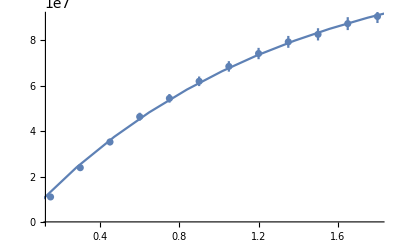

```mathematica
Needs["ErrorBarPlots`"]
tryfit=NonlinearModelFit[AtomNumberNoErr[[1]],{N0*(1-Exp[-t/τ])},{N0,τ},{t},MaxIterations->20000]
p1=ErrorListPlot[AtomNumberwithErr[[1]],PlotRange->{All,{0,All}}];
f1=Plot[tryfit[t],{t,-1,8},PlotRange->{All,{0,All}}];
Show[p1,f1]
```